```mathematica
Vaje iz Računalniška orodja v matematiki, 6.november 2018
```

### 1. NALOGA

```mathematica
d = Daljica[{-1,1}, {3,-1}]
d2=Daljica[{-1,-1}, {3,1}]
d3=Daljica[{-1,2}, {3,0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_,BB_]] := Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA,BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

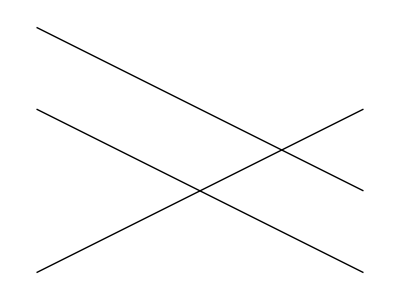

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika,List[d]]]
Narisi[d,d2,d3]
```

```mathematica
ClearAll[x,y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1,y1,x2,y2, k,n}, {x1,y1}= AA; {x2,y2}=BB; k=(y2-y1)/(x2-x1) ;n=n/.First[Solve[y1==k*x1+n, n]]; y== k*x+n]
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
y
```

y

### 2. NALOGA

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] :=Module[{resitev}, resitev = Solve[{AA+r*(BB-AA)==CC+s*(DD-CC), 0≤ r,r≤ 1,0≤ s,s≤ 1}, {r,s}];If[resitev=={},{},First[AA+r*(BB-AA)/.resitev]]]
Presek[d,d2]
```

{1,0}

```mathematica
Presek[d,d3]
```

{}

### 3. NALOGA

```mathematica
ClearAll[Slika]
```

```mathematica
m1 =Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]] := Line[{{0,0},{1,1},{0,3},{-1,2},First[m1]}]
Slika [m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

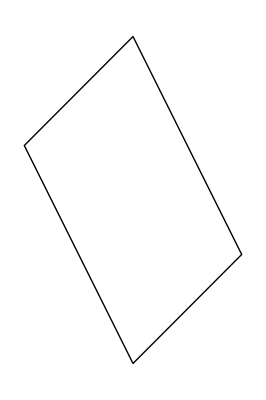

```mathematica
Narisi[m1_]:= Graphics[Slika[m1]]
Narisi[m1]
```

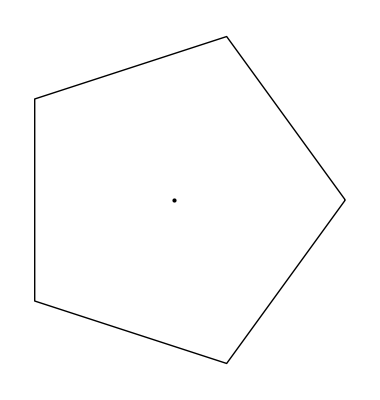

```mathematica
PravilniNKotnik[n_,r_] := Graphics[{Line[Table[{r *Cos[(2π*i)/n],r*Sin[(2π*i)/n]},{i,0,n}] ],Point[{0,0}]}]
p5 = PravilniNKotnik[5,2]
```

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
Manipulate[PravilniNKotnik[5,2,phi],{phi,1.57,33}]
```

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, {2, 2}, 1]
```

```mathematica
Partition[{1,2,3,4,5},2]
```

{{1,2},{3,4}}

```mathematica
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{2,3},{3,4},{4,5}}

### 4. NALOGA

```mathematica
ClearAll[d,m1]
```

```mathematica
d = Daljica[{-1,1},{3,-1}];
d2 = Daljica[{-1,-1},{3,1}];
d3 = Daljica[{-1, 2},{3, 0}];
m1;
```

```mathematica
Presek[m_Mnogokotnik[AA_, BB_], d_Daljica[CC_,DD_]]:= Module[{a, b},
a = Daljice[m1];
b = d;
resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1}, {x, y}]]
```

```mathematica
Presek[m1, d]
```

```mathematica
{}
```

```mathematica
Presek[m1, d2]
```

```mathematica
{}
```

### 5. NALOGA

```mathematica
ClearAll[f,a,b,d]
```

```mathematica
VsiPari[f_,sez1_, sez2_] := Flatten[Outer[f,sez1, sez2],1]
VsiPari[f, {1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
q= Outer[f, {1, 2,3 },{a, b}]
```

{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

```mathematica
Flatten[q]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}]
```

{b,2,1,3,4,f,g,h}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 1]
```

{b,2,1,3,{4},f,{g,h}}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 2]
```

{b,2,1,3,4,f,g,h}

```mathematica
Outer[{b, 2},{1, 3, {4}},{f, {g, h}}]
```

{{{b,2}[1,f],{{b,2}[1,g],{b,2}[1,h]}},{{b,2}[3,f],{{b,2}[3,g],{b,2}[3,h]}},{{{b,2}[4,f],{{b,2}[4,g],{b,2}[4,h]}}}}

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
m2 = Mnogokotnik[{0,0},{1,1},{0,3},{-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m3 = Mnogokotnik[{0,1},{1,2},{2,3},{-5, 2}]
```

Mnogokotnik[{0,1},{1,2},{2,3},{-5,2}]

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:= VsiPari[f, m1, m2]
```

```mathematica
Presek[m1, m2]
Presek[m1, m3]
```

Presek[m1,Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]]

Presek[m1,Mnogokotnik[{0,1},{1,2},{2,3},{-5,2}]]

```mathematica
?Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

### 6. NALOGA

a) Izračunaj vektorski produkt v1 in v2, če imaš podane 3 točke.

```mathematica
ClearAll[A,B]
```

```mathematica
AA:={-5,6,-4}
BB:={-4,-1,2}
CC:={-1,-2,4} 
v1[AA_,BB_] := BB-AA
v2[AA_,CC_] := CC-AA
v1[AA,BB]
v2[AA,CC]
```

{1,-7,6}

{4,-8,8}

b) Nariši vektorja v1, v2

```mathematica
vektorji = {{AA, BB},{AA, CC}}
```

{{{-5,6,-4},{-4,-1,2}},{{-5,6,-4},{-1,-2,4}}}

```mathematica
Graphics3D[Map[Line, vektorji ]]
```

-Graphics3D-